# Synchronizing Metronomes (Entrainment)

## Analytic and Numerical Treatment

Ethan Knox

## Analytical Treatment

### Hanging Pendula on a Moving Platform

y_1=-l_1cos(θ_1)
y_2=-l_2cos(θ_2)

```mathematica
y1=-l1 Cos[θ1[x,y,t]]
y2=-l2 Cos[θ2[x,y,t]]
```

-l1 Cos[θ1[x,y,t]]

-l2 Cos[θ2[x,y,t]]

q_l=-g(m_1 sin(θ_1)+m_2 sin(θ_2))δ(y-h)
q_r=-g(m_1 sin(θ_1)+m_2 sin(θ_2))δ(y-h)
q_t=g(m_1 cos(θ_1)δ(x-x_1)+m_2 cos(θ_2)δ(x-x_2))

```mathematica
ql=-g (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) DiracDelta[y-h]
qr=-g (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) DiracDelta[y-h]
qt=g (m1 Cos[θ1[x,y,t]]DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2])
(*wl=wr[y,t]*)
```

-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])

-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])

g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2])

w_l=w_r
T_l=1/2 μ ((ẇ)_l)^2, T_r=1/2 μ((ẇ)_r)^2, T_t=1/2 μ((ẇ)_t)^2,
 T_1=1/2 I_1((θ̇)_1)^2, T_2=1/2 I_2((θ̇)_2)^2

V_1=1/2 EI((∂^2 w_l)/(∂y^2))^2-q_l w_l, V_r=1/2 EI((∂^2 w_r)/(∂y^2))^2-q_r w_r, V_t=1/2 EI((∂^2 w_t)/(∂x^2))^2-q_t w_t,
 V_1=m_1 gy_1, V_2=m_2 gy_2

```mathematica
Tl=1/2 μ D[wl[x,y,t],t]^2
Tri=1/2 μ D[wr[x,y,t],t]^2
Tt=1/2 μ D[wt[x,y,t],t]^2
T1=1/2 I1 D[θ1[x,y,t],t]^2
T2=1/2 I2 D[θ2[x,y,t],t]^2
Vl=1/2 EI D[wl[x,y,t],{y,2}]^2-ql wl[x,y,t]
Vr=1/2 EI D[wr[x,y,t],{y,2}]^2-qr wr[x,y,t]
Vt=1/2 EI D[wt[x,y,t],{x,2}]^2-qt wt[x,y,t]
V1=m1 g y1
V2=m2 g y2
```

1/2 μ (wl^(0,0,1)[x,y,t])^2

1/2 μ (wr^(0,0,1)[x,y,t])^2

1/2 μ (wt^(0,0,1)[x,y,t])^2

1/2 I1 (θ1^(0,0,1)[x,y,t])^2

1/2 I2 (θ2^(0,0,1)[x,y,t])^2

g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wl[x,y,t]+1/2 EI (wl^(0,2,0)[x,y,t])^2

g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wr[x,y,t]+1/2 EI (wr^(0,2,0)[x,y,t])^2

-g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2]) wt[x,y,t]+1/2 EI (wt^(2,0,0)[x,y,t])^2

-g l1 m1 Cos[θ1[x,y,t]]

-g l2 m2 Cos[θ2[x,y,t]]

T=T_l+T_r+T_t+T_1+T_2
V=V_l+V_r+V_t+V_1+V_2
L=T-V

```mathematica
T=Tl+Tri+Tt+T1+T2
V=Vl+Vr+Vt+V1+V2
L=T-V
```

1/2 μ (wl^(0,0,1)[x,y,t])^2+1/2 μ (wr^(0,0,1)[x,y,t])^2+1/2 μ (wt^(0,0,1)[x,y,t])^2+1/2 I1 (θ1^(0,0,1)[x,y,t])^2+1/2 I2 (θ2^(0,0,1)[x,y,t])^2

-g l1 m1 Cos[θ1[x,y,t]]-g l2 m2 Cos[θ2[x,y,t]]+g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wl[x,y,t]+g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wr[x,y,t]-g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2]) wt[x,y,t]+1/2 EI (wl^(0,2,0)[x,y,t])^2+1/2 EI (wr^(0,2,0)[x,y,t])^2+1/2 EI (wt^(2,0,0)[x,y,t])^2

g l1 m1 Cos[θ1[x,y,t]]+g l2 m2 Cos[θ2[x,y,t]]-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wl[x,y,t]-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]]) wr[x,y,t]+g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2]) wt[x,y,t]+1/2 μ (wl^(0,0,1)[x,y,t])^2+1/2 μ (wr^(0,0,1)[x,y,t])^2+1/2 μ (wt^(0,0,1)[x,y,t])^2+1/2 I1 (θ1^(0,0,1)[x,y,t])^2+1/2 I2 (θ2^(0,0,1)[x,y,t])^2-1/2 EI (wl^(0,2,0)[x,y,t])^2-1/2 EI (wr^(0,2,0)[x,y,t])^2-1/2 EI (wt^(2,0,0)[x,y,t])^2

EL_l→ (∂L)/(∂w_l)-d/dt((∂L)/(∂(ẇ)_l))+∂^2/(∂y^2)((∂L)/(∂((∂^2 w_l)/(∂y^2))))=0
EL_r→ (∂L)/(∂w_r)-d/dt((∂L)/(∂(ẇ)_r))+∂^2/(∂y^2)((∂L)/(∂((∂^2 w_r)/(∂y^2))))=0
EL_t→ (∂L)/(∂w_t)-d/dt((∂L)/(∂(ẇ)_t))+∂^2/(∂x^2)((∂L)/(∂((∂^2 w_t)/(∂x^2))))=0
EL_1→ (∂L)/(∂θ_1)-d/dt((∂L)/(∂(θ̇)_1))=0
EL_2→ (∂L)/(∂θ_2)-d/dt((∂L)/(∂(θ̇)_2))=0

```mathematica
ELl=D[L, wl[x,y,t]]-D[D[L, D[wl[x,y,t], t]], t]+D[D[L, D[wl[x,y,t], y,y]], y,y]==0
ELr=D[L, wr[x,y,t]]-D[D[L, D[wr[x,y,t], t]], t]+D[D[L, D[wr[x,y,t], y,y]], y,y]==0
ELt=D[L, wt[x,y,t]]-D[D[L, D[wt[x,y,t], t]], t]+D[D[L, D[wt[x,y,t], x,x]], x,x]==0
EL1=D[L, θ1[x,y,t]]-D[D[L, D[θ1[x,y,t], t]], t]==0
EL2=D[L, θ2[x,y,t]]-D[D[L, D[θ2[x,y,t], t]], t]==0
```

-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])-μ wl^(0,0,2)[x,y,t]-EI wl^(0,4,0)[x,y,t]==0

-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])-μ wr^(0,0,2)[x,y,t]-EI wr^(0,4,0)[x,y,t]==0

g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2])-μ wt^(0,0,2)[x,y,t]-EI wt^(4,0,0)[x,y,t]==0

-g l1 m1 Sin[θ1[x,y,t]]-g m1 Cos[θ1[x,y,t]] DiracDelta[-h+y] wl[x,y,t]-g m1 Cos[θ1[x,y,t]] DiracDelta[-h+y] wr[x,y,t]-g m1 DiracDelta[x-x1] Sin[θ1[x,y,t]] wt[x,y,t]-I1 θ1^(0,0,2)[x,y,t]==0

-g l2 m2 Sin[θ2[x,y,t]]-g m2 Cos[θ2[x,y,t]] DiracDelta[-h+y] wl[x,y,t]-g m2 Cos[θ2[x,y,t]] DiracDelta[-h+y] wr[x,y,t]-g m2 DiracDelta[x-x2] Sin[θ2[x,y,t]] wt[x,y,t]-I2 θ2^(0,0,2)[x,y,t]==0

```mathematica
pdes={ELl,ELr,ELt,EL1,EL2};
ics={wl[x,y,t]==wr[x,y,t],wl[x,y,0]==0,wr[x,y,0]==0,θ1[x,y,0]==θ10,θ2[x,y,0]==θ20};
```

```mathematica
Reduce[pdes]
```

```mathematica
DSolve[pdes,{wl,wr,wt,θ1,θ2},{x,y,t}]
```

DSolve[{-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])-μ wl^(0,0,2)[x,y,t]-EI wl^(0,4,0)[x,y,t]==0,-g DiracDelta[-h+y] (m1 Sin[θ1[x,y,t]]+m2 Sin[θ2[x,y,t]])-μ wr^(0,0,2)[x,y,t]-EI wr^(0,4,0)[x,y,t]==0,g (m1 Cos[θ1[x,y,t]] DiracDelta[x-x1]+m2 Cos[θ2[x,y,t]] DiracDelta[x-x2])-μ wt^(0,0,2)[x,y,t]-EI wt^(4,0,0)[x,y,t]==0,-g l1 m1 Sin[θ1[x,y,t]]-g m1 Cos[θ1[x,y,t]] DiracDelta[-h+y] wl[x,y,t]-g m1 Cos[θ1[x,y,t]] DiracDelta[-h+y] wr[x,y,t]-g m1 DiracDelta[x-x1] Sin[θ1[x,y,t]] wt[x,y,t]-I1 θ1^(0,0,2)[x,y,t]==0,-g l2 m2 Sin[θ2[x,y,t]]-g m2 Cos[θ2[x,y,t]] DiracDelta[-h+y] wl[x,y,t]-g m2 Cos[θ2[x,y,t]] DiracDelta[-h+y] wr[x,y,t]-g m2 DiracDelta[x-x2] Sin[θ2[x,y,t]] wt[x,y,t]-I2 θ2^(0,0,2)[x,y,t]==0},{wl,wr,wt,θ1,θ2},{x,y,t}]

```mathematica
wl[y,t]==wr[y,t]
```

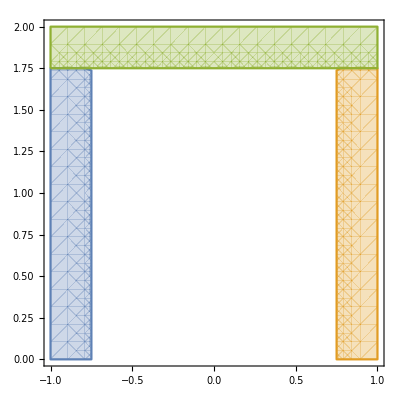

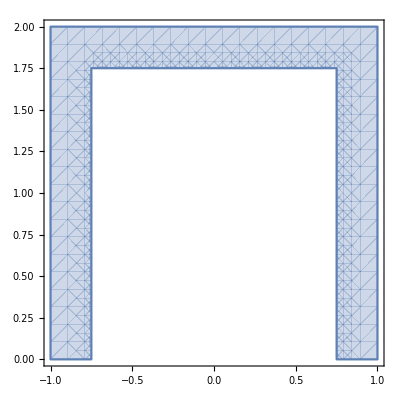

ToBoundaryMesh::femtemnbb: The bounds for ImplicitRegion[-1≤x≤-0.75&&0≤y≤1.75&&0.75≤x≤1&&0≤y≤1.75&&-1≤x≤1&&1.75≤y≤2&&-1≤x≤1&&0≤y≤2,{x,y}] are {{∞,-∞},{∞,-∞}}. Unless finite numeric bounds are specified, the mesh generation will constrain the region to have finite bounds.

ToBoundaryMesh::femtemnm: A mesh could not be generated.

$Failed

$Failed[Wireframe]

```mathematica
w=2;dw=0.25;h=2;dh=0.25;
bleft:=-w/2<=x≤-w/2+dw&&0≤y≤h-dh
bright:=w/2-dw<=x≤w/2&&0≤y≤h-dh
btop:=-w/2<=x≤w/2&&h-dh≤y≤h
Bleft=ImplicitRegion[bleft,{x,y}];
Bright=ImplicitRegion[bright,{x,y}];
Btop=ImplicitRegion[btop,{x,y}];
RegionPlot[{bleft,bright,btop},{x,-w/2,w/2},{y,0,h}]
RegionPlot[bleft||bright||btop,{x,-w/2,w/2},{y,0,h}]
```

```mathematica
wl[t_]:=q0[t]-w/2
wr[t_]:=q0[t]+w/2
s1l2[t_]:=(q1[t]-wl[t])^2
s1r2[t_]:=(wr[t]-q1[t])^2
s2l2[t_]:=(q2[t]-wl[t])^2
s2r2[t_]:=(wr[t]-q2[t])^2

V[t_]:=1/2 (k1l s1l2[t]+k1r s1r2[t]+k2l s2l2[t]+k2r s2r2[t])
T[t_]:=1/2 (M q0'[t]^2+m1 q1'[t]^2+m2 q2'[t]^2)
L[t_]:=T[t]-V[t]

U[t_]:=1/2 (k0 q0'[t]^2+k1 q1'[t]^2+k2 q2'[t]^2)-A1 Sin[ω1 t] q1'[t]-A2 Sin[ω2 t] q2'[t]

eqn0[t_]:=ELg[L[t],0,U[t],q0'[t],q0[t]]
eqn1[t_]:=ELg[L[t],0,U[t],q1'[t],q1[t]]
eqn2[t_]:=ELg[L[t],0,U[t],q2'[t],q2[t]]
ode:=FullSimplify[{eqn0[t],eqn1[t],eqn2[t]}]
ics:={q1'[0]==0,q2'[0]==0,q0'[0]==0,q1[0]==q10,q2[0]==q20,q0[0]==q00}
```

## Numerical Treatment

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
k0=0.0;k1=0.0;k2=0.0;
m1=1;m2=1;
M=10;w=2;
k1l=1;k1r=1;
k2l=1;k2r=1;
q10=w/(4+0.001);q20=w/(4-0.001);q00=0;
ω1=1;ω2=1;
A1=1;A2=1;
time=500;
frac=0.9;
```

```mathematica
ode
ics
```

{2 q0[t]+5 q0''[t]==q1[t]+q2[t],2 q0[t]+Sin[t]==2 q1[t]+q1''[t],2 q0[t]+Sin[t]==2 q2[t]+q2''[t]}

{q1'[0]==0,q2'[0]==0,q0'[0]==0,q1[0]==0.499875,q2[0]==0.500125,q0[0]==0}

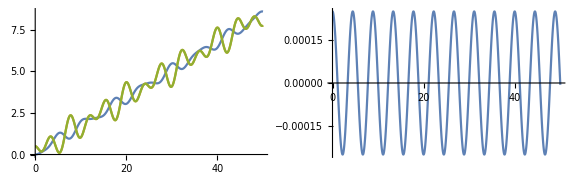

C:/users/ethan/documents/code/coolestplot.pdf

```mathematica
sol=First[NDSolve[Flatten[{ode,ics}],{q0[t],q1[t],q2[t]},{t,0,time}]];
q0[t_]:=Evaluate[q0[t]/.sol]
q1[t_]:=Evaluate[q1[t]/.sol]
q2[t_]:=Evaluate[q2[t]/.sol]

(*Plot[{q1[t],q2[t]},{t,0,(1-frac) time},PlotRange->All,ImageSize->Large]
Export["C:/users/ethan/documents/code/coolplotbeginning.pdf",%]
Plot[{q1[t],q2[t]},{t,0,frac time},PlotRange->All,ImageSize->Large]
Export["C:/users/ethan/documents/code/coolplotend.pdf",%]*)
GraphicsRow[{Plot[{q0[t],q1[t],q2[t]},{t,0,(1-frac) time},PlotRange->All],Plot[q2[t]-q1[t],{t,0,(1-frac) time},PlotRange->All]},ImageSize->Large]
Export["C:/users/ethan/documents/code/coolestplot.pdf",%]
(*Plot[Abs[q2[t]-q1[t]],{t,0,(1-frac) time},ImageSize->Large]
Plot[Abs[q2[t]-q1[t]],{t,frac time,time},ImageSize->Large]*)

(*GraphicsRow[{Plot[q1[t],{t,frac time,time}],Plot[q2[t]-q1[t],{t,frac time,time}]},ImageSize->Large]*)
(*GraphicsRow[{Plot[q0[t]/.sol,{t,frac time,time}],Plot[q1[t]/.sol,{t,frac time,time}],Plot[q2[t]/.sol,{t,frac time,time}],Plot[q2[t]-q1[t]/.sol,{t,frac time,time}]},ImageSize->Large]*)
Quit[]

min=Min[Map[q0[#]&,Table[t,{t,0,time,0.1}]]]
max=Max[Map[q0[#]&,Table[t,{t,0,time,0.1}]]]
frames=Table[Graphics[{Brown,Thick,Rectangle[{wl[t],-1},{wr[t],1}],Gray,Rectangle[{wl[t]+0.25,0.25-0},{wr[t]-0.25,1-0.25}],Rectangle[{wl[t]+0.25,0.25-1},{wr[t]-0.25,0-0.25}],Darker[Blue],Disk[{q1[t],0.5},.1],Disk[{q2[t],-0.5},.1]},PlotRange->{{q0[t]-w,q0[t]+w},{-2.5,2.5}}],{t,0,time,.1}];
ListAnimate[frames,AnimationRunning->False]
Export["C:/users/ethan/documents/code/test.avi",%]
Quit[]
```

```mathematica
Quit[]
```

Holonomic:
	∃f∍f(q_i,t)=0
Non-Holonomic:
	Isn’t Holonomic
Semi-Holonomic:
	∃f∍a((q̇)_i,q_i,t)=∑_(i=1)^n [a_li(q,t)(q̇)_i]+a_l0(q,t)=0
Use Holonomic constraints to rewrite coordinates to generalized ones

Euler-Lagrange Equations:
	d/dt((∂L)/(∂(q̇)_i))-(∂L)/(∂q_i)=0
Lagrange Equations:
Always:
	d/dt((∂L)/(∂(q̇)_i))-(∂L)/(∂q_i)=Q_i
More Descriptive:
	d/dt((∂L)/(∂(q̇)_i))-(∂L)/(∂q_i)=Q_i-(∂F)/(∂(q̇)_i)+∑_(l=1)^m [λ_l a_li]
where,
	∑_(i=1)^n [a_li(q,t)(q̇)_i]+a_l0(q,t)=0
	
If the generalized forces can also come from a function U(q,q̇) such that:
	Q_j=d/dt(∂U)/(∂(q̇)_j)-(∂U)/(∂q_j)
Then this is still sufficient to create the Lagrangian L=T-U

```mathematica
D[L[x,y,t], wl[y,t]]-D[D[L[x,y,t], D[wl[y,t], t]], t]+D[D[L[x,y,t], D[wl[y,t], y,y]], y,y]
```

0

```mathematica
f[t_]:=c Sin[x[t]]
D[D[f[t],t],D[f[t],t]]
```

General::ivar: c Cos[x[t]] x'[t] is not a valid variable.

∂_(c Cos[x[t]] x'[t]) (c Cos[x[t]] x'[t])